```mathematica
UniformEvens=Import[FileNameJoin[{NotebookDirectory[],"uniformevens.csv"}],"csv"];
UniformOdds=Import[FileNameJoin[{NotebookDirectory[],"uniformodds.csv"}],"csv"];

LinearHardEvens=Import[FileNameJoin[{NotebookDirectory[],"linearhardevens.csv"}],"csv"];
LinearHardOdds=Import[FileNameJoin[{NotebookDirectory[],"linearhardodds.csv"}],"csv"];
LinearSoftEvens=Import[FileNameJoin[{NotebookDirectory[],"linearsoftevens.csv"}],"csv"];
LinearSoftOdds=Import[FileNameJoin[{NotebookDirectory[],"linearsoftodds.csv"}],"csv"];
LinearBorder = Graphics[Line[{{0,0},{10,10}}]];

CircleHardEvens=Import[FileNameJoin[{NotebookDirectory[],"circlehardevens.csv"}],"csv"];
CircleHardOdds=Import[FileNameJoin[{NotebookDirectory[],"circlehardodds.csv"}],"csv"];
CircleSoftEvens=Import[FileNameJoin[{NotebookDirectory[],"circlesoftevens.csv"}],"csv"];
CircleSoftOdds=Import[FileNameJoin[{NotebookDirectory[],"circlesoftodds.csv"}],"csv"];
CircleBorder = Graphics[Circle[{2,2},2]];

TwoCircleHardEvens=Import[FileNameJoin[{NotebookDirectory[],"twocirclehardevens.csv"}],"csv"];
TwoCircleHardOdds=Import[FileNameJoin[{NotebookDirectory[],"twocirclehardodds.csv"}],"csv"];
TwoCircleSoftEvens=Import[FileNameJoin[{NotebookDirectory[],"twocirclesoftevens.csv"}],"csv"];
TwoCircleSoftOdds=Import[FileNameJoin[{NotebookDirectory[],"twocirclesoftodds.csv"}],"csv"];
TwoCircleBorder = Graphics[{Circle[{2,2},2],Circle[{6,6},Sqrt[2]]}];

TwoSphereHardEvens=Import[FileNameJoin[{NotebookDirectory[],"twospherehardevens.csv"}],"csv"];
TwoSphereHardOdds=Import[FileNameJoin[{NotebookDirectory[],"twospherehardodds.csv"}],"csv"];
TwoSphereSoftEvens=Import[FileNameJoin[{NotebookDirectory[],"twospheresoftevens.csv"}],"csv"];
TwoSphereSoftOdds=Import[FileNameJoin[{NotebookDirectory[],"twospheresoftodds.csv"}],"csv"];

TwoSphereHard100KEvens=Import[FileNameJoin[{NotebookDirectory[],"twospherehard100kevens.csv"}],"csv"];
TwoSphereHard100KOdds=Import[FileNameJoin[{NotebookDirectory[],"twospherehard100kodds.csv"}],"csv"];
TwoSphereSoft100KEvens=Import[FileNameJoin[{NotebookDirectory[],"twospheresoft100Kevens.csv"}],"csv"];
TwoSphereSoft100KOdds=Import[FileNameJoin[{NotebookDirectory[],"twospheresoft100Kodds.csv"}],"csv"];
```

```mathematica
plotWithColors[data_,border_]:=Block[{signal, background,signalPlot, backgroundPlot},
signal = List[];
background = List[];

For[i = 1, i ≤ Length[data],i++,
If[data⟦i⟧⟦3⟧ == 1,AppendTo[signal,Drop[data⟦i⟧,-1]], AppendTo[background,Drop[data⟦i⟧,-1]]]
];

signalPlot = ListPlot[signal,PlotStyle->Blue,PlotRange->{{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2"},AspectRatio->1];
backgroundPlot = ListPlot[background, PlotStyle->Red,PlotRange->{{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2"},AspectRatio->1];
Show[signalPlot, backgroundPlot, border]
]
```

```mathematica
plotWithColors3D[data_]:=Block[{signal, background,signalPlot, backgroundPlot},
signal = List[];
background = List[];

For[i = 1, i ≤ Length[data],i++,
If[data⟦i⟧⟦4⟧ == 1,AppendTo[signal,Drop[data⟦i⟧,-1]], AppendTo[background,Drop[data⟦i⟧,-1]]]
];

signalPlot = ListPointPlot3D[signal,PlotStyle->Blue,PlotRange->{{0,10},{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2","Feature 3"},AspectRatio->1];
backgroundPlot = ListPointPlot3D[background, PlotStyle->Red,PlotRange->{{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2", "Feature 3"},AspectRatio->1];

Show[signalPlot,backgroundPlot]
]
```

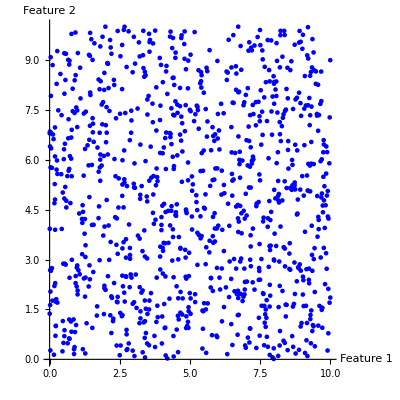

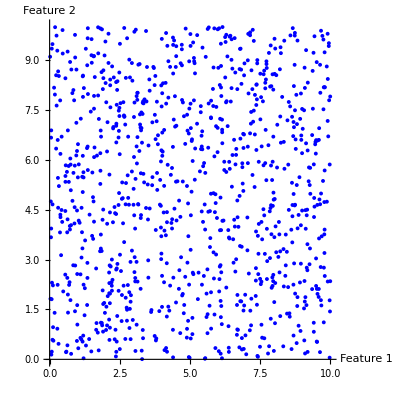

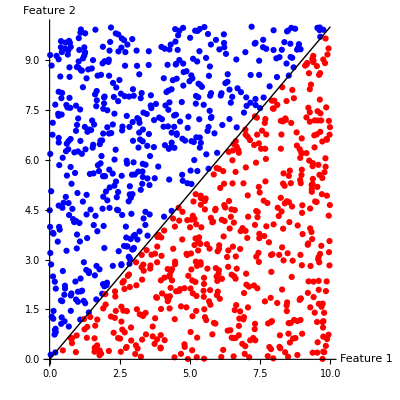

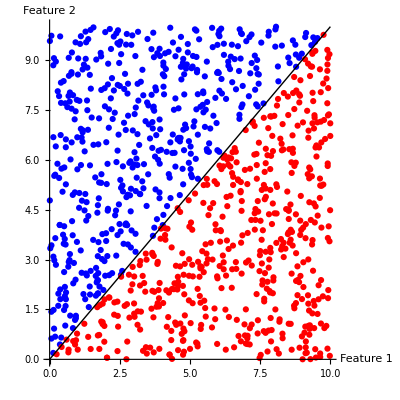

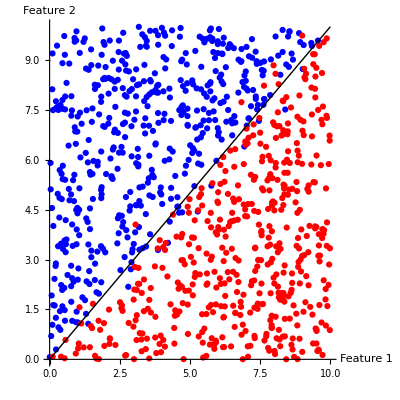

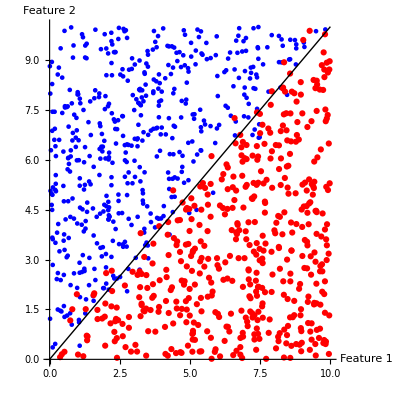

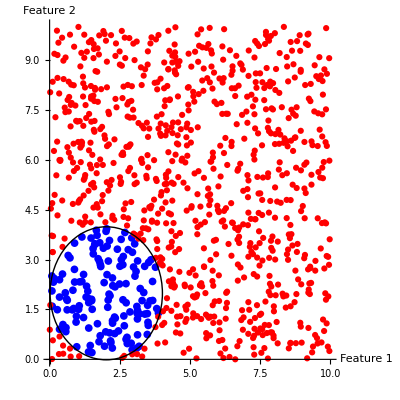

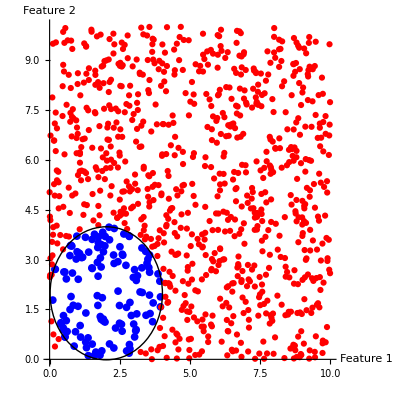

-Graphics3D-

-Graphics3D-

-Graphics3D-

«5 more identical outputs»

```mathematica
plotWithColors[UniformEvens]
plotWithColors[UniformOdds]

plotWithColors[LinearHardEvens,LinearBorder]
plotWithColors[LinearHardOdds,LinearBorder]
plotWithColors[LinearSoftEvens,LinearBorder]
plotWithColors[LinearSoftOdds,LinearBorder]

plotWithColors[CircleHardEvens,CircleBorder]
plotWithColors[CircleHardOdds,CircleBorder]
plotWithColors[CircleSoftEvens,CircleBorder]
plotWithColors[CircleSoftOdds,CircleBorder]

plotWithColors[TwoCircleHardEvens,TwoCircleBorder]
plotWithColors[TwoCircleHardOdds,TwoCircleBorder]
plotWithColors[TwoCircleSoftEvens,TwoCircleBorder]
plotWithColors[TwoCircleSoftOdds,TwoCircleBorder]

plotWithColors3D[TwoSphereHardEvens]
plotWithColors3D[TwoSphereHardOdds]
plotWithColors3D[TwoSphereSoftEvens]
plotWithColors3D[TwoSphereSoftOdds]

plotWithColors3D[TwoSphereHard100KEvens]
plotWithColors3D[TwoSphereHard100KOdds]
plotWithColors3D[TwoSphereSoft100KEvens]
plotWithColors3D[TwoSphereSoft100KOdds]
```